```mathematica
a=Table[If[i==j==0,1,0],{i,-128,128},{j,-128,128}];n=1;While[n<128,a=Table[If[i≠1&&i≠257&&j≠1&&j≠257&&a[[i-1,j-1]]+a[[i,j-1]]+a[[i+1,j-1]]+a[[i-1,j]]+a[[i+1,j]]+a[[i-1,j+1]]+a[[i,j+1]]+a[[i+1,j+1]]==1,1,a[[i,j]]],{i,1,257},{j,1,257}];n++];ArrayPlot[a]
```

-Graphics-

```mathematica
Checkboard=a;
update[1,2]:=1;
update[_,3]:=1;
update[_,_]:=0;
SetAttributes[update,Listable];
Dynamic[ArrayPlot[Checkboard=update[Checkboard,Plus@@Map[RotateRight[Checkboard,#]&,{{-1,-1},{-1,0},{-1,1},{0,-1},{0,1},{1,-1},{1,0},{1,1}}]]]]
```

```mathematica
a=Table[If[i==j==0,1,0],{i,-128,128},{j,-128,128}];n=1;While[n<128,a=Table[If[i≠1&&i≠257&&j≠1&&j≠257&&(a[[i-1,j-1]]+a[[i,j-1]]+a[[i+1,j-1]]+a[[i-1,j]]+a[[i+1,j]]+a[[i-1,j+1]]+a[[i,j+1]]+a[[i+1,j+1]]==1||a[[i-1,j-1]]+a[[i,j-1]]+a[[i+1,j-1]]+a[[i-1,j]]+a[[i+1,j]]+a[[i-1,j+1]]+a[[i,j+1]]+a[[i+1,j+1]]==2),1,a[[i,j]]],{i,1,257},{j,1,257}];n++];ArrayPlot[a]
```

-Graphics-

```mathematica
Checkboard=a;
update[1,2]:=1;
update[_,3]:=1;
update[_,_]:=0;
SetAttributes[update,Listable];
Dynamic[ArrayPlot[Checkboard=update[Checkboard,Plus@@Map[RotateRight[Checkboard,#]&,{{-1,-1},{-1,0},{-1,1},{0,-1},{0,1},{1,-1},{1,0},{1,1}}]]]]
```

```mathematica
a=Table[If[i==j==0,1,0],{i,-128,128},{j,-128,128}];n=1;While[n<128,a=Table[If[i≠1&&i≠257&&j≠1&&j≠257&&OddQ[a[[i-1,j-1]]+a[[i,j-1]]+a[[i+1,j-1]]+a[[i-1,j]]+a[[i+1,j]]+a[[i-1,j+1]]+a[[i,j+1]]+a[[i+1,j+1]]],1,a[[i,j]]],{i,1,257},{j,1,257}];n++];ArrayPlot[a]
```

-Graphics-

```mathematica
Checkboard=a;
update[1,2]:=1;
update[_,3]:=1;
update[_,_]:=0;
SetAttributes[update,Listable];
Dynamic[ArrayPlot[Checkboard=update[Checkboard,Plus@@Map[RotateRight[Checkboard,#]&,{{-1,-1},{-1,0},{-1,1},{0,-1},{0,1},{1,-1},{1,0},{1,1}}]]]]
```

```mathematica
a=Table[If[i==j==0,1,0],{i,-128,128},{j,-128,128}];n=1;While[n<128,a=Table[If[i≠1&&i≠257&&j≠1&&j≠257,b=a[[i-1,j-1]]+a[[i,j-1]]+a[[i+1,j-1]]+a[[i-1,j]]+a[[i+1,j]]+a[[i-1,j+1]]+a[[i,j+1]]+a[[i+1,j+1]];If[0<b<3,1,0],0],{i,1,257},{j,1,257}];n++];ArrayPlot[a]
```

-Graphics-

```mathematica
Checkboard=a;
update[1,2]:=1;
update[_,3]:=1;
update[_,_]:=0;
SetAttributes[update,Listable];
Dynamic[ArrayPlot[Checkboard=update[Checkboard,Plus@@Map[RotateRight[Checkboard,#]&,{{-1,-1},{-1,0},{-1,1},{0,-1},{0,1},{1,-1},{1,0},{1,1}}]]]]
Beep[]
```

```mathematica
a=Table[If[i==j==0,1,0],{i,-128,128},{j,-128,128}];n=1;While[n<128,a=Table[If[i≠1&&i≠257&&j≠1&&j≠257,b=a[[i-1,j-1]]+a[[i,j-1]]+a[[i+1,j-1]]+a[[i-1,j]]+a[[i+1,j]]+a[[i-1,j+1]]+a[[i,j+1]]+a[[i+1,j+1]];
If[0<b<3∨6<b<9,1,0],0],{i,1,257},{j,1,257}];n++];ArrayPlot[a]
Beep[]
```

-Graphics-

```mathematica
Checkboard=a;
update[1,2]:=1;
update[_,3]:=1;
update[_,_]:=0;
SetAttributes[update,Listable];
Dynamic[ArrayPlot[Checkboard=update[Checkboard,Plus@@Map[RotateRight[Checkboard,#]&,{{-1,-1},{-1,0},{-1,1},{0,-1},{0,1},{1,-1},{1,0},{1,1}}]]]]
Beep[]
```

```mathematica
Checkboard=ImageData[
Binarize[
Rasterize[Style["赵海珠",FontSize->200,FontFamily->"SimSun"]]]];
update[1,2]:=1;
update[_,3]:=1;
update[_,_]:=0;
SetAttributes[update,Listable];
Dynamic[ArrayPlot[Checkboard=update[Checkboard,Plus@@Map[RotateRight[Checkboard,#]&,{{-1,-1},{-1,0},{-1,1},{0,-1},{0,1},{1,-1},{1,0},{1,1}}]]]]
Beep[]
```

```mathematica
Checkboard=ImageData[
Binarize[-Graphics-]];
update[1,2]:=1;
update[_,3]:=1;
update[_,_]:=0;
SetAttributes[update,Listable];
Dynamic[ArrayPlot[Checkboard=update[Checkboard,Plus@@Map[RotateRight[Checkboard,#]&,{{-1,-1},{-1,0},{-1,1},{0,-1},{0,1},{1,-1},{1,0},{1,1}}]]]]
Beep[]
```

```mathematica
Rasterize[Style["赵",FontSize->20,FontFamily->"SimSun"]]
Graphics[ImageHistogram[Rasterize[Style["赵",FontSize->20,FontFamily->"SimSun"]]]]
```

-Graphics-

```mathematica
Rasterize[Style["赵",FontSize->20,FontFamily->"SimSun"]]
```

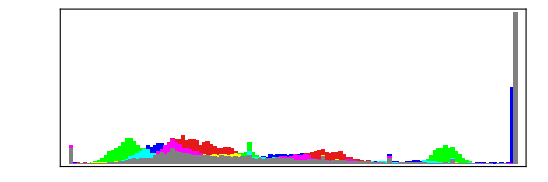

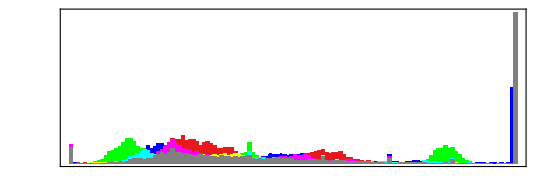

```mathematica
ImageHistogram[-Graphics-]
ImageHistogram[-Graphics-]
```

```mathematica
a=ImageData[ImageHistogram[-Graphics-,Appearance->"Separated"]];b=ImageData[ImageHistogram[-Graphics-,Appearance->"Separated"]];
```

```mathematica
Image[a-b]
```

-Graphics-

```mathematica
a=ImageData[-Graphics-];b=ImageData[-Graphics-];
```

```mathematica
Dimensions[a]
Dimensions[b]
```

{135,468,3}

{143,475,3}

```mathematica
{Dimensions[a],Dimensions[b]}ᵀ
```

{{135,143},{468,475},{3,3}}

```mathematica
{Dimensions[a],Dimensions[b]}ᵀ
Map[Min,{Dimensions[a],Dimensions[b]}ᵀ]
```

{{135,143},{468,475},{3,3}}

{135,468,3}

```mathematica
#
```

```mathematica
A[[p,All]]/.p->{1,2}
```

Part::pspec: Part specification p is neither an integer nor a list of integers.

{{135,468,3},{143,475,3}}

```mathematica
Matrix
```

```mathematica
a=ImageData[-Graphics-];
b=ImageData[-Graphics-];
size=Map[Min,{Dimensions[a],Dimensions[b]}ᵀ];
n=2;
a=a[[;;size[[1]],3;;2+size[[2]],;;size[[3]]]];
b=b[[;;size[[1]],;;size[[2]],;;size[[3]]]];
Image[a-b]
```

-Graphics-

```mathematica
a=ImageData[-Graphics-];
b=ImageData[-Graphics-];
{Dimensions[a],Dimensions[b]}
```

(265 | 274 | 3
265 | 271 | 3)

```mathematica
try=ImageData[-Graphics-];
ImageAdjust[ImageSubtract[Image[try[[185;;470,10;;397]]],Image[try[[185;;470,403;;790]]]],{-0.5,0.5}]
```

-Graphics-

```mathematica
ImageSubtract[-Graphics-,-Graphics-]
```

-Graphics-

```mathematica
Checkboard=ImageData[
Binarize[ImageSubtract[Image[a],Image[b]],0.05]];
Image[%]
```

-Graphics-

```mathematica
Checkboard=ImageData[
Binarize[ImageSubtract[Image[a],Image[b]],.1]];
update[_,2]:=0;
update[_,1]:=0;
update[_,_]:=1;
SetAttributes[update,Listable];
Image[Checkboard=update[Checkboard,Plus@@Map[RotateRight[Checkboard,#]&,{{-1,-1},{-1,0},{-1,1},{0,-1},{0,1},{1,-1},{1,0},{1,1}}]]]
Beep[]
```

-Graphics-

```mathematica
n+1;;5+n
```

2;;6

```mathematica
a={{1,2,3,4},{1,4,7,8},{3,6,5,8}}
size={2,3};
a[[;;size[[1]],;;size[[2]]]]
```

(1 | 2 | 3 | 4
1 | 4 | 7 | 8
3 | 6 | 5 | 8)

(1 | 2 | 3
1 | 4 | 7)

No more memory available.
Mathematica kernel has shut down.
Try quitting other applications and then retry.